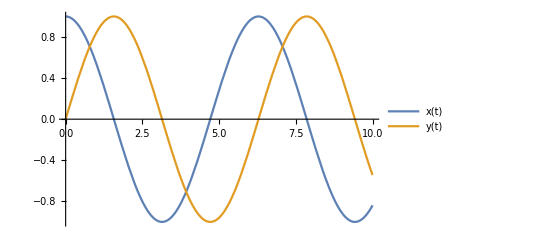

```mathematica
(*定义微分方程组*)eqns={x'[t]==-y[t],y'[t]==x[t]};
(*定义初始条件*)
inits={x[0]==1,y[0]==0};
(*求解微分方程组*)
sol=NDSolve[{eqns,inits},{x,y},{t,0,10}];
(*绘制数值解*)
Plot[Evaluate[{x[t],y[t]}/. sol],{t,0,10},PlotLegends->{"x(t)","y(t)"}]
```